## Definitions

```mathematica
Sx={{0,(√3)/2,0,0},{(√3)/2,0,1,0},{0,1,0,(√3)/2},{0,0,(√3)/2,0}};
Sy={{0,(√3)/(2ⅈ),0,0},{(√3)/(-2ⅈ),0,1/ⅈ,0},{0,-1/ⅈ,0,(√3)/(2ⅈ)},{0,0,(-√3)/(2ⅈ),0}};
Sz={{3/2,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,-3/2}};
Γx=Sx.Sx.Sx-41/20 Sx;
Γy=Sy.Sy.Sy-41/20 Sy;
Γz=Sz.Sz.Sz-41/20 Sz;
```

```mathematica
Sx//MatrixForm
Sy//MatrixForm
Sz//MatrixForm
Γx//MatrixForm
Γy//MatrixForm
Γz//MatrixForm
```

(0 | (√3)/2 | 0 | 0
(√3)/2 | 0 | 1 | 0
0 | 1 | 0 | (√3)/2
0 | 0 | (√3)/2 | 0)

(0 | -(ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 0 | -ⅈ | 0
0 | ⅈ | 0 | -(ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 0)

(3/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -3/2)

(0 | -(3 √3)/20 | 0 | 3/4
-(3 √3)/20 | 0 | 9/20 | 0
0 | 9/20 | 0 | -(3 √3)/20
3/4 | 0 | -(3 √3)/20 | 0)

(0 | (3 ⅈ √3)/20 | 0 | (3 ⅈ)/4
-(3 ⅈ √3)/20 | 0 | -(9 ⅈ)/20 | 0
0 | (9 ⅈ)/20 | 0 | (3 ⅈ √3)/20
-(3 ⅈ)/4 | 0 | -(3 ⅈ √3)/20 | 0)

(3/10 | 0 | 0 | 0
0 | -9/10 | 0 | 0
0 | 0 | 9/10 | 0
0 | 0 | 0 | -3/10)

```mathematica
Tr[Sx.Sx]
Tr[Sx.Γx]
Tr[Γx.Γx]
Tr[Sx.Sy]
Tr[Γx.Γy]
Tr[Sx.Γy]
```

5

0

9/5

0

0

0

```mathematica
H[δ_,kx_,ky_,kz_]:=v (kx Γx+ky Γy+kz Γz)+v δ (kx Sx+ky Sy+kz Sz);
H[δ,kx,ky,kz]//MatrixForm
```

((3 kz v)/10+(3 kz v δ)/2 | (-(3 √3 kx)/20+3/20 ⅈ √3 ky) v+((√3 kx)/2-1/2 ⅈ √3 ky) v δ | 0 | ((3 kx)/4+(3 ⅈ ky)/4) v
(-(3 √3 kx)/20-3/20 ⅈ √3 ky) v+((√3 kx)/2+1/2 ⅈ √3 ky) v δ | -(9 kz v)/10+(kz v δ)/2 | ((9 kx)/20-(9 ⅈ ky)/20) v+(kx-ⅈ ky) v δ | 0
0 | ((9 kx)/20+(9 ⅈ ky)/20) v+(kx+ⅈ ky) v δ | (9 kz v)/10-(kz v δ)/2 | (-(3 √3 kx)/20+3/20 ⅈ √3 ky) v+((√3 kx)/2-1/2 ⅈ √3 ky) v δ
((3 kx)/4-(3 ⅈ ky)/4) v | 0 | (-(3 √3 kx)/20-3/20 ⅈ √3 ky) v+((√3 kx)/2+1/2 ⅈ √3 ky) v δ | -(3 kz v)/10-(3 kz v δ)/2)

```mathematica
PropagatorS[ω_,kx_,ky_,kz_,δ_]:=Simplify[Inverse[-ⅈ ω IdentityMatrix[4]+H[δ,kx,ky,kz]]];
PropagatorS[ω,kx,ky,kz,0]//MatrixForm
```

((5 (486 kz^3 v^3+27 kx^2 v^2 (9 kz v+20 ⅈ ω)+27 ky^2 v^2 (9 kz v+20 ⅈ ω)+1620 ⅈ kz^2 v^2 ω+600 kz v ω^2+2000 ⅈ ω^3))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (15 √3 v (27 kx^3 v^2+108 ⅈ kx^2 ky v^2+ky (-27 ⅈ ky^2 v^2+27 ⅈ kz^2 v^2-60 kz v ω+100 ⅈ ω^2)-kx (108 ky^2 v^2+27 kz^2 v^2+60 ⅈ kz v ω+100 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (45 √3 v^2 (4 ⅈ kx ky (9 kz v+5 ⅈ ω)+kx^2 (27 kz v+40 ⅈ ω)-ky^2 (27 kz v+40 ⅈ ω)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (15 v (81 kx^3 v^2+162 ⅈ kx^2 ky v^2+ⅈ ky (81 ky^2 v^2+405 kz^2 v^2+500 ω^2)+kx (162 ky^2 v^2+405 kz^2 v^2+500 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2))
(15 √3 v (27 kx^3 v^2-108 ⅈ kx^2 ky v^2+ky (27 ⅈ ky^2 v^2-27 ⅈ kz^2 v^2+60 kz v ω-100 ⅈ ω^2)-kx (108 ky^2 v^2+27 kz^2 v^2+60 ⅈ kz v ω+100 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (5 (9 kx^2 v^2 (-117 kz v+140 ⅈ ω)+9 ky^2 v^2 (-117 kz v+140 ⅈ ω)+2 (-81 kz^3 v^3+90 ⅈ kz^2 v^2 ω-900 kz v ω^2+1000 ⅈ ω^3)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (45 v (45 kx^3 v^2-90 ⅈ kx^2 ky v^2-ⅈ ky (45 ky^2 v^2+9 kz^2 v^2+100 ω^2)+kx (90 ky^2 v^2+9 kz^2 v^2+100 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | -(45 √3 v^2 (kx^2 (27 kz v-40 ⅈ ω)+ky^2 (-27 kz v+40 ⅈ ω)+4 kx ky (9 ⅈ kz v+5 ω)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2))
(45 √3 v^2 (kx^2 (27 kz v+40 ⅈ ω)-ky^2 (27 kz v+40 ⅈ ω)+4 kx ky (-9 ⅈ kz v+5 ω)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (45 v (45 kx^3 v^2+90 ⅈ kx^2 ky v^2+ⅈ ky (45 ky^2 v^2+9 kz^2 v^2+100 ω^2)+kx (90 ky^2 v^2+9 kz^2 v^2+100 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (5 (9 kx^2 v^2 (117 kz v+140 ⅈ ω)+9 ky^2 v^2 (117 kz v+140 ⅈ ω)+2 (81 kz^3 v^3+90 ⅈ kz^2 v^2 ω+900 kz v ω^2+1000 ⅈ ω^3)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (15 √3 v (27 kx^3 v^2+108 ⅈ kx^2 ky v^2+ky (-27 ⅈ ky^2 v^2+27 ⅈ kz^2 v^2+60 kz v ω+100 ⅈ ω^2)-kx (108 ky^2 v^2+27 kz^2 v^2-60 ⅈ kz v ω+100 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2))
(15 v (81 kx^3 v^2-162 ⅈ kx^2 ky v^2-ⅈ ky (81 ky^2 v^2+405 kz^2 v^2+500 ω^2)+kx (162 ky^2 v^2+405 kz^2 v^2+500 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | -(45 √3 v^2 (4 kx ky (-9 ⅈ kz v-5 ω)+kx^2 (27 kz v-40 ⅈ ω)+ky^2 (-27 kz v+40 ⅈ ω)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | (15 √3 v (27 kx^3 v^2-108 ⅈ kx^2 ky v^2+ⅈ ky (27 ky^2 v^2-27 kz^2 v^2+60 ⅈ kz v ω-100 ω^2)-kx (108 ky^2 v^2+27 kz^2 v^2-60 ⅈ kz v ω+100 ω^2)))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)) | -(5 (486 kz^3 v^3+27 kx^2 v^2 (9 kz v-20 ⅈ ω)+27 ky^2 v^2 (9 kz v-20 ⅈ ω)-1620 ⅈ kz^2 v^2 ω+600 kz v ω^2-2000 ⅈ ω^3))/(729 kx^4 v^4+729 ky^4 v^4+729 kz^4 v^4+9000 kz^2 v^2 ω^2+10000 ω^4+9 ky^2 (567 kz^2 v^4+1000 v^2 ω^2)+9 kx^2 (567 ky^2 v^4+567 kz^2 v^4+1000 v^2 ω^2)))

## Numerical RG

### Self Energy

```mathematica
RgV[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Cos[θ] 5/9(Tr[PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Γz]+Tr[PropagatorS[-ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Γz])/.v->1,{ω,-Infinity,Infinity},{ϕ,0,2π},{θ,0,π}]]
RgDV[δ_]:=Re[NIntegrate[Sin[θ]/(2π)^4 Cos[θ] 1/5(Tr[PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Sz]+Tr[PropagatorS[-ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ].Sz])/.v->1,{ω,-Infinity,Infinity},{ϕ,0,2π},{θ,0,π}]]
```

```mathematica
BetaD[δ_]:=RgDV[δ]-δ RgV[δ]
```

```mathematica
BetaD[0]
```

0.00244057

{-1.,0.000434766}

{-0.95,0.000463173}

{-0.9,0.000464115}

{-0.85,0.000440552}

{-0.8,0.00039596}

{-0.75,0.000334496}

{-0.7,0.000261161}

{-0.65,0.000182123}

{-0.6,0.000105083}

{-0.55,0.0000398534}

{-0.5,-8.16229×10^-7}

{-0.45,3.45236×10^-11}

{-0.4,0.000065288}

{-0.35,0.000227051}

{-0.3,0.000531021}

{-0.25,0.00104447}

{-0.2,0.00186954}

{-0.15,0.00254057}

{-0.1,0.00273581}

{-0.05,0.00266619}

{0.,0.00244057}

{0.05,0.00212027}

{0.1,0.00174199}

{0.15,0.00132857}

{0.2,0.000894618}

{0.25,0.00044963}

{0.3,8.67362×10^-19}

{0.35,-0.000449711}

{0.4,-0.000896046}

{0.45,-0.00133617}

{0.5,-0.00176765}

{0.55,-0.00218833}

{0.6,-0.00259625}

{0.65,-0.00298965}

{0.7,-0.00336695}

{0.75,-0.00372671}

{0.8,-0.00406762}

{0.85,-0.00438851}

{0.9,-0.0046883}

{0.95,-0.00496599}

{1.,-0.0052207}

{{-1.,0.000434766},{-0.95,0.000463173},{-0.9,0.000464115},{-0.85,0.000440552},{-0.8,0.00039596},{-0.75,0.000334496},{-0.7,0.000261161},{-0.65,0.000182123},{-0.6,0.000105083},{-0.55,0.0000398534},{-0.5,-8.16229×10^-7},{-0.45,3.45236×10^-11},{-0.4,0.000065288},{-0.35,0.000227051},{-0.3,0.000531021},{-0.25,0.00104447},{-0.2,0.00186954},{-0.15,0.00254057},{-0.1,0.00273581},{-0.05,0.00266619},{0.,0.00244057},{0.05,0.00212027},{0.1,0.00174199},{0.15,0.00132857},{0.2,0.000894618},{0.25,0.00044963},{0.3,8.67362×10^-19},{0.35,-0.000449711},{0.4,-0.000896046},{0.45,-0.00133617},{0.5,-0.00176765},{0.55,-0.00218833},{0.6,-0.00259625},{0.65,-0.00298965},{0.7,-0.00336695},{0.75,-0.00372671},{0.8,-0.00406762},{0.85,-0.00438851},{0.9,-0.0046883},{0.95,-0.00496599},{1.,-0.0052207}}

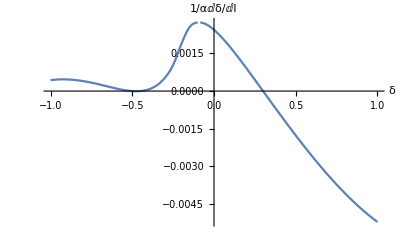

```mathematica
data1={};
For[i=0,i<41,i++,y=BetaD[-1+0.05i];data1=AppendTo[data1,{-1+0.05i,y}];Print[{-1+0.05i,y}]]
data1
ListLinePlot[data1,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

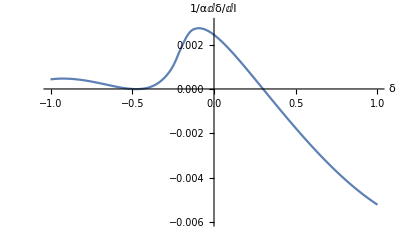

```mathematica
ListLinePlot[data1,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2,PlotRange->{{-1,1},{-0.006,0.003}}]
```

{-0.55,0.0000398534}

{-0.545,0.0000344398}

{-0.54,0.0000292809}

{-0.535,0.0000243979}

{-0.53,0.0000198008}

{-0.525,0.0000155067}

{-0.52,0.000011533}

{-0.515,7.896×10^-6}

{-0.51,4.61334×10^-6}

{-0.505,1.70264×10^-6}

{-0.5,-8.16229×10^-7}

{-0.495,-2.92568×10^-6}

{-0.49,-4.6054×10^-6}

{-0.485,-5.83519×10^-6}

{-0.48,-6.59433×10^-6}

{-0.475,-6.86053×10^-6}

{-0.47,-6.61285×10^-6}

{-0.465,-5.82659×10^-6}

{-0.46,-4.47838×10^-6}

{-0.455,-2.54516×10^-6}

{-0.45,3.45236×10^-11}

{-0.445,3.18449×10^-6}

{-0.44,7.03034×10^-6}

{-0.435,0.0000115711}

{-0.43,0.0000168294}

{-0.425,0.0000228414}

{{-0.55,0.0000398534},{-0.545,0.0000344398},{-0.54,0.0000292809},{-0.535,0.0000243979},{-0.53,0.0000198008},{-0.525,0.0000155067},{-0.52,0.000011533},{-0.515,7.896×10^-6},{-0.51,4.61334×10^-6},{-0.505,1.70264×10^-6},{-0.5,-8.16229×10^-7},{-0.495,-2.92568×10^-6},{-0.49,-4.6054×10^-6},{-0.485,-5.83519×10^-6},{-0.48,-6.59433×10^-6},{-0.475,-6.86053×10^-6},{-0.47,-6.61285×10^-6},{-0.465,-5.82659×10^-6},{-0.46,-4.47838×10^-6},{-0.455,-2.54516×10^-6},{-0.45,3.45236×10^-11},{-0.445,3.18449×10^-6},{-0.44,7.03034×10^-6},{-0.435,0.0000115711},{-0.43,0.0000168294},{-0.425,0.0000228414}}

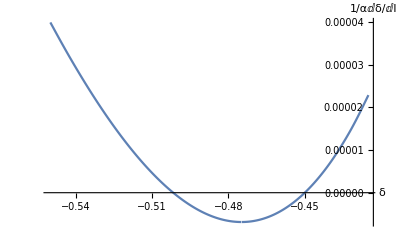

```mathematica
data2={};
For[i=0,i<26,i++,y=BetaD[-0.55+0.005i];data2=AppendTo[data2,{-0.55+0.005i,y}];Print[{-0.55+0.005i,y}]]
data2
ListLinePlot[data2,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

{0.29,0.0000900581}

{0.291,0.0000810531}

{0.292,0.000072048}

{0.293,0.0000630425}

{0.294,0.0000540369}

{0.295,0.000045031}

{0.296,0.000036025}

{0.297,0.0000270188}

{0.298,0.0000180126}

{0.299,9.00632×10^-6}

{0.3,0.}

{0.301,-9.00632×10^-6}

{0.302,-0.0000180126}

{0.303,-0.0000270188}

{0.304,-0.000036025}

{0.305,-0.000045031}

{0.306,-0.0000540369}

{0.307,-0.0000630425}

{0.308,-0.000072048}

{0.309,-0.0000810532}

{0.31,-0.0000900582}

{{0.29,0.0000900581},{0.291,0.0000810531},{0.292,0.000072048},{0.293,0.0000630425},{0.294,0.0000540369},{0.295,0.000045031},{0.296,0.000036025},{0.297,0.0000270188},{0.298,0.0000180126},{0.299,9.00632×10^-6},{0.3,0.},{0.301,-9.00632×10^-6},{0.302,-0.0000180126},{0.303,-0.0000270188},{0.304,-0.000036025},{0.305,-0.000045031},{0.306,-0.0000540369},{0.307,-0.0000630425},{0.308,-0.000072048},{0.309,-0.0000810532},{0.31,-0.0000900582}}

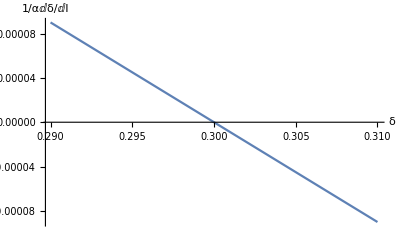

```mathematica
data3={};
For[i=0,i<21,i++,y=BetaD[0.29+0.001i];data3=AppendTo[data3,{0.29+0.001i,y}];Print[{0.29+0.001i,y}]]
data3
ListLinePlot[data3,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

{-0.51,4.61334×10^-6}

{-0.509,4.00093×10^-6}

{-0.508,3.40343×10^-6}

{-0.507,2.82123×10^-6}

{-0.506,2.25443×10^-6}

{-0.505,1.70264×10^-6}

{-0.504,1.16692×10^-6}

{-0.503,6.47332×10^-7}

{-0.502,1.43329×10^-7}

{-0.501,-3.44598×10^-7}

{-0.5,-8.16229×10^-7}

{-0.499,-1.2715×10^-6}

{-0.498,-1.71015×10^-6}

{-0.497,-2.13252×10^-6}

{-0.496,-2.53766×10^-6}

{-0.495,-2.92568×10^-6}

{-0.494,-3.29662×10^-6}

{-0.493,-3.65029×10^-6}

{-0.492,-3.98638×10^-6}

{-0.491,-4.30466×10^-6}

{-0.49,-4.6054×10^-6}

{{-0.51,4.61334×10^-6},{-0.509,4.00093×10^-6},{-0.508,3.40343×10^-6},{-0.507,2.82123×10^-6},{-0.506,2.25443×10^-6},{-0.505,1.70264×10^-6},{-0.504,1.16692×10^-6},{-0.503,6.47332×10^-7},{-0.502,1.43329×10^-7},{-0.501,-3.44598×10^-7},{-0.5,-8.16229×10^-7},{-0.499,-1.2715×10^-6},{-0.498,-1.71015×10^-6},{-0.497,-2.13252×10^-6},{-0.496,-2.53766×10^-6},{-0.495,-2.92568×10^-6},{-0.494,-3.29662×10^-6},{-0.493,-3.65029×10^-6},{-0.492,-3.98638×10^-6},{-0.491,-4.30466×10^-6},{-0.49,-4.6054×10^-6}}

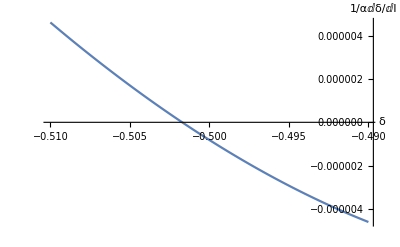

```mathematica
data4={};
For[i=0,i<21,i++,y=BetaD[-0.51+0.001i];data4=AppendTo[data4,{-0.51+0.001i,y}];Print[{-0.51+0.001i,y}]]
data4
ListLinePlot[data4,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

{-0.46,-4.47838×10^-6}

{-0.459,-4.13748×10^-6}

{-0.458,-3.77628×10^-6}

{-0.457,-3.39004×10^-6}

{-0.456,-2.97972×10^-6}

{-0.455,-2.54516×10^-6}

{-0.454,-2.087×10^-6}

{-0.453,-1.60197×10^-6}

{-0.452,-1.09273×10^-6}

{-0.451,-5.59088×10^-7}

{-0.45,3.45236×10^-11}

{-0.449,5.91333×10^-7}

{-0.448,1.19449×10^-6}

{-0.447,1.82792×10^-6}

{-0.446,2.49373×10^-6}

{-0.445,3.18449×10^-6}

{-0.444,3.89726×10^-6}

{-0.443,4.63685×10^-6}

{-0.442,5.40939×10^-6}

{-0.441,6.206×10^-6}

{-0.44,7.03034×10^-6}

{{-0.46,-4.47838×10^-6},{-0.459,-4.13748×10^-6},{-0.458,-3.77628×10^-6},{-0.457,-3.39004×10^-6},{-0.456,-2.97972×10^-6},{-0.455,-2.54516×10^-6},{-0.454,-2.087×10^-6},{-0.453,-1.60197×10^-6},{-0.452,-1.09273×10^-6},{-0.451,-5.59088×10^-7},{-0.45,3.45236×10^-11},{-0.449,5.91333×10^-7},{-0.448,1.19449×10^-6},{-0.447,1.82792×10^-6},{-0.446,2.49373×10^-6},{-0.445,3.18449×10^-6},{-0.444,3.89726×10^-6},{-0.443,4.63685×10^-6},{-0.442,5.40939×10^-6},{-0.441,6.206×10^-6},{-0.44,7.03034×10^-6}}

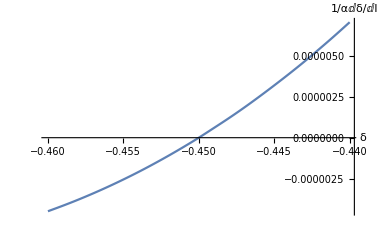

```mathematica
data5={};
For[i=0,i<21,i++,y=BetaD[-0.46+0.001i];data5=AppendTo[data5,{-0.46+0.001i,y}];Print[{-0.46+0.001i,y}]]
data5
ListLinePlot[data5,AxesLabel->{"δ","1/αⅆδ/ⅆl"},InterpolationOrder->2]
```

### Polarization diagram

```mathematica
BetaG[δ_]:=NIntegrate[Re[Sin[θ]/(2π)^4 Simplify[D[Tr[PropagatorS[ω,Sin[θ]Cos[ϕ]+q,Sin[θ]Sin[ϕ],Cos[θ],δ].PropagatorS[ω,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ],δ]],{q,2}]/.q->0]/.v->1],{ω,-Infinity,Infinity},{θ,0,π},{ϕ,0,2π}];
```

```mathematica
BetaG[0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0987548 and 1.82659×10^-7 for the integral and error estimates.

-0.0987548

```mathematica
data6={};
For[i=0,i<41,i++,y=BetaG[-1+0.05i];data5=AppendTo[data6,{-1+0.05i,y}];Print[{-1+0.05i,y}]]
data6
ListLinePlot[data6,AxesLabel->{"δ","v/g^3ⅆg/ⅆl"},InterpolationOrder->2]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.468246 and 0.0000679399 for the integral and error estimates.

{-1.,-0.468246}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.379187 and 0.0000455956 for the integral and error estimates.

{-0.95,-0.379187}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.320273 and 0.000022506 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{-0.9,-0.320273}

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

{-0.85,-0.278674}

{-0.8,-0.248025}

{-0.75,-0.224847}

{-0.7,-0.207143}

{-0.65,-0.193768}

{-0.6,-0.184156}

{-0.55,-0.178224}

{-0.5,-0.176442}

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

{-0.45,-0.180127}

{-0.4,-0.192301}

{-0.35,-0.220348}

{-0.3,-0.286707}

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

{-0.25,-0.503915}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-0.2,-1.1078×10^204}

{-0.15,-0.431162}

{-0.1,-0.207863}

{-0.05,-0.13456}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.,-0.0987548}

{0.05,-0.078023}

{0.1,-0.0649458}

{0.15,-0.0563734}

{0.2,-0.0507343}

{0.25,-0.0471396}

{0.3,-0.0450316}

{0.35,-0.0440334}

{0.4,-0.0438787}

{0.45,-0.0443777}

{0.5,-0.0453966}

{0.55,-0.0468441}

{0.6,-0.0486617}

{0.65,-0.0508164}

{0.7,-0.053295}

{0.75,-0.0561012}

{0.8,-0.0592529}

{0.85,-0.0627819}

{0.9,-0.0667343}

{0.95,-0.0711725}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

$Aborted

$Aborted

$Aborted

```mathematica
ParallelTable[{BetaG[-0.22+0.05(i-1)]},{i,1,2}]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.17496 and 0.0000730068 for the integral and error estimates.

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.730583 and 0.0000328302 for the integral and error estimates.

{{-1.17496},{-0.730583}}